```mathematica
Needs["DorisAlgorithmCompactCase`"]
```

(-3+x) (-2+x) (-1+x)^3 (1+x)^3 (2+x) (3+x)

True

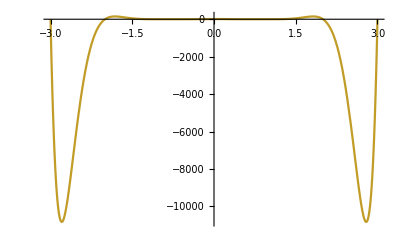

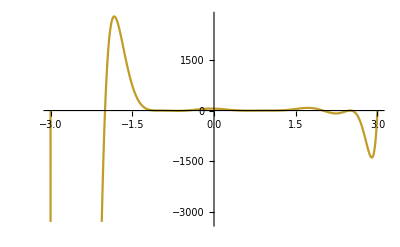

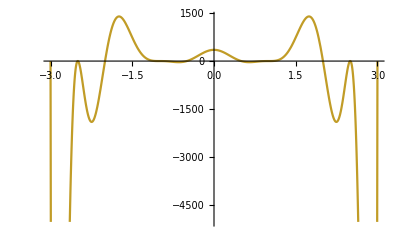

```mathematica
infix=(x+1/2)(x-1/2);
outfix=(x+3)(x+2)(x+1)^3(x-1)^3(x-2)(x-3)
g=-outfix infix;
templateS1=a^2((x-b)^2+c^2);
DorisAlgorithmCompactCase[x,infix,{g}]
Plot[-g,{x,-3,3}]
Plot[-g (x-(2+3)/2)^2,{x,-3,3}]
Plot[-g (x-(2+3)/2)^2(x-(-2-3)/2)^2,{x,-3,3}]
```

```mathematica
Series[1+templateS1 outfix,{x,-1/2,10}]
Series[1+templateS1 outfix,{x,1/2,10}]
```

(1-(14175 a^2 ((-1/2-b)^2+c^2))/1024)-675/512 (a^2 (1+25 b+46 b^2+46 c^2)) (x+1/2)-27/512 (a^2 (-723-1642 b+658 b^2+658 c^2)) (x+1/2)^2+a^2 (-15525/256-8883/256 (-1-2 b)+2049/16 ((-1/2-b)^2+c^2)) (x+1/2)^3+a^2 (-8883/256+2049/16 (-1-2 b)+2489/32 ((-1/2-b)^2+c^2)) (x+1/2)^4+a^2 (2049/16+2489/32 (-1-2 b)-1039/8 ((-1/2-b)^2+c^2)) (x+1/2)^5+a^2 (2489/32-1039/8 (-1-2 b)-167/8 ((-1/2-b)^2+c^2)) (x+1/2)^6+a^2 (-1039/8-167/8 (-1-2 b)+49 ((-1/2-b)^2+c^2)) (x+1/2)^7+a^2 (-167/8+49 (-1-2 b)-19/4 ((-1/2-b)^2+c^2)) (x+1/2)^8+a^2 (49-19/4 (-1-2 b)-5 ((-1/2-b)^2+c^2)) (x+1/2)^9+a^2 (-19/4-5 (-1-2 b)+(-1/2-b)^2+c^2) (x+1/2)^10+O[x+1/2]^11

(1-(14175 a^2 ((1/2-b)^2+c^2))/1024)+675/512 a^2 (1-25 b+46 b^2+46 c^2) (x-1/2)-27/512 (a^2 (-723+1642 b+658 b^2+658 c^2)) (x-1/2)^2+a^2 (15525/256-8883/256 (1-2 b)-2049/16 ((1/2-b)^2+c^2)) (x-1/2)^3+a^2 (-8883/256-2049/16 (1-2 b)+2489/32 ((1/2-b)^2+c^2)) (x-1/2)^4+a^2 (-2049/16+2489/32 (1-2 b)+1039/8 ((1/2-b)^2+c^2)) (x-1/2)^5+a^2 (2489/32+1039/8 (1-2 b)-167/8 ((1/2-b)^2+c^2)) (x-1/2)^6+a^2 (1039/8-167/8 (1-2 b)-49 ((1/2-b)^2+c^2)) (x-1/2)^7+a^2 (-167/8-49 (1-2 b)-19/4 ((1/2-b)^2+c^2)) (x-1/2)^8+a^2 (-49-19/4 (1-2 b)+5 ((1/2-b)^2+c^2)) (x-1/2)^9+a^2 (-19/4+5 (1-2 b)+(1/2-b)^2+c^2) (x-1/2)^10+O[x-1/2]^11

```mathematica
sol=FindInstance[(1-(14175 a^2 ((-1/2-b)^2+c^2))/1024)==0&&-675/512 (a^2 (1+25 b+46 b^2+46 c^2)) <0&&(1-(14175 a^2 ((1/2-b)^2+c^2))/1024)==0&&675/512 a^2 (1-25 b+46 b^2+46 c^2)>0,{a,b,c},Reals][[1]]
```

{a→-33/64,b→0,c→(√(1340641/7))/2970}

```mathematica
s1=templateS1/.sol
Reduce[s1<0,x]
s0=infix(1+s1 outfix);
Reduce[s0<0,x]
s0+s1 g//Simplify
```

(1089 (1340641/61746300+x^2))/4096

False

Root-3.00Root[-183980124+1324728743 #1^2-1973972460 #1^4+1137992562 #1^6-242790896 #1^8+15436575 #1^10&,1]-2.9999728542173085<x<Root-2.00Root[-183980124+1324728743 #1^2-1973972460 #1^4+1137992562 #1^6-242790896 #1^8+15436575 #1^10&,2]-2.0017187505334983||Root-0.429Root[-183980124+1324728743 #1^2-1973972460 #1^4+1137992562 #1^6-242790896 #1^8+15436575 #1^10&,3]-0.4293585910807117<x<Root0.429Root[-183980124+1324728743 #1^2-1973972460 #1^4+1137992562 #1^6-242790896 #1^8+15436575 #1^10&,4]0.4293585910807117||Root2.00Root[-183980124+1324728743 #1^2-1973972460 #1^4+1137992562 #1^6-242790896 #1^8+15436575 #1^10&,5]2.0017187505334983<x<Root3.00Root[-183980124+1324728743 #1^2-1973972460 #1^4+1137992562 #1^6-242790896 #1^8+15436575 #1^10&,6]2.9999728542173085

-1/4+x^2

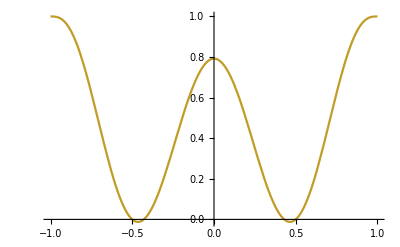

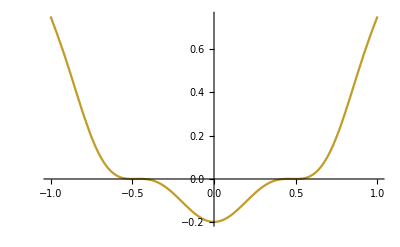

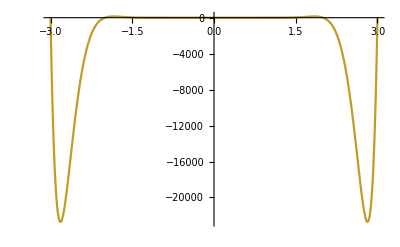

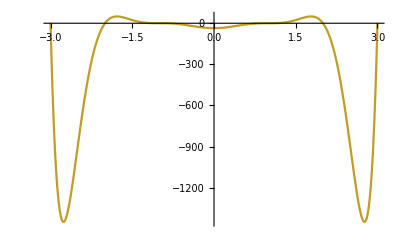

```mathematica
Plot[1+s1 outfix,{x,-1,1}]
Plot[infix(1+s1 outfix),{x,-1,1}]
Plot[infix(1+s1 outfix),{x,-3,3}]
Plot[outfix,{x,-3,3}]
```

```mathematica
Plot[outfix,{x,-3,3}]
```

-Graphics-